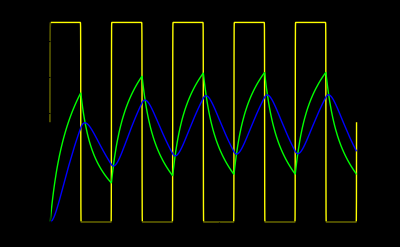

```mathematica
R1=R2=10000;
R3=10^6;
C1=33*10^-9;
C2=22*10^-9;

uZ[t]=amplituda*(1+Tanh[100 Sin[2*Pi*frekvence*t]])/2;
amplituda=3.3;
frekvence=917 ;

uzel1=iU[t]==iR1[t];
uzel2=iR1[t]==iC1[t]+iR2[t];
uzel3=iR2[t]==iC2[t]+iR3[t];

rez1=u1[t]-u2[t]==iR1[t]*R1;
rez2=u2[t]-u3[t]==iR2[t]*R2;
rez3=u3[t]==iR3[t]*R3;
cond1=iC1[t]==C1*u2'[t];
cond2=iC2[t]==C2*u3'[t];
zdroj=uZ[t]==u1[t];
podm1=u2[0]==0;
podm2=u3[0]==0;

rovnice={uzel1,uzel2,uzel3,rez1,rez2,rez3,cond1,cond2,zdroj,podm1,podm2};
nezname={iU[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],u1[t],u2[t],u3[t]};
vysledek=NDSolve[rovnice,nezname,{t,0,5*1/frekvence},StartingStepSize->10^-10];

Plot[{u1[t]/.vysledek,u2[t]/.vysledek,u3[t]/.vysledek},{t,0,5*1/frekvence},PlotStyle->{{Yellow,Thick},{Green,Thick},{Blue,Thick}},Background->Black,AxesStyle->White,AxesLabel->{"t [s]","u [V]"}]
```